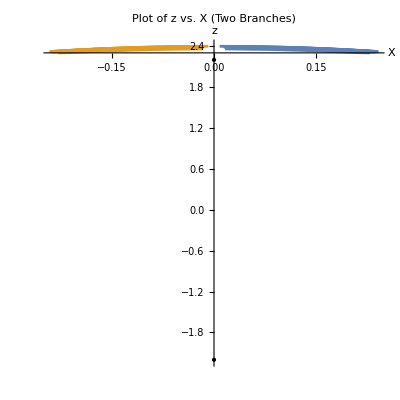

```mathematica
(*Case I*)(*Variables set up*)B= 0.75;
e=1.4;
b=2.2;

(*Relations to main parameters*)
g=Sqrt[e^2+B^2-1];

eeta[b_,e_]:=b/(1-e^2);
p=(1-e^2);

f=eeta[b,e];

d0[f_,e_]:=2/((1-f^2*(1-e^2))+Sqrt[(1-f^2*(1+e^2))^2-4*f^4*e^2]);
deltaV=f^2*d0[f,e];
eStar=e*((1+f^2*d0[f,e])/(1+f^2*d0[f,e]*e^2));

kS1=Sqrt[((1-f^2*(1-e^2)-Sqrt[(1+f^2*(1-e^2))^2-4*f^2*B^2]))/(1-f^2*(1-e^2)+Sqrt[(1+f^2*(1-e^2))^2-4*f^2*B^2])];
deltaS=(-2*f*B)/(1+f^2*(1-e^2)+Sqrt[(1+f^2*(1-e^2))^2-4*f^2*B^2]);
kv=Sqrt[f^2*e^2*(1+2*f^2+f^4*(2+e^2))];
jv=Sqrt[(1-f^2*(1-e^2)+Sqrt[(1-f^2*(1-e^2))^2-4*f^2*e^2])/(2*Sqrt[(1+f^2*(1-e^2))^2-4*f^2*e^2])];
kS0=((2*Sqrt[b*g]-Sqrt[(b+g)^2-B^2])/(2*Sqrt[b*g]+Sqrt[(b+g)^2-B^2]));
deltaSS=(((-b-g)*(b+B-g))/((b+g)^2+B*(b-g)+2*Sqrt[b*g*((b+g)^2-B^2)]));

deltaR=-(((b+e)*(1-(b-e)))/((b+e)^2-(b-e)+2*Sqrt[b*e]*Sqrt[(b+e)^2-1]));
kR=((2*Sqrt[b*e]-Sqrt[(b+e)^2-1])/(2*Sqrt[b*e]+Sqrt[(b+e)^2-1]));

(*for 1-e<=b<=B-g*)
jr1=Sqrt[(2*Sqrt[b*e]+Sqrt[(b+e)^2-1])^2/(2*((1-e^2+b^2)+Sqrt[(1-e^2+b^2)^2-4*b^2*B^2]))];
(*for B-g<=b<=1+e*)
jr0=(2*Sqrt[b*e]+Sqrt[(b+e)^2-1])/(2*Sqrt[b*g]+Sqrt[(b+g)^2-B^2]);

(*Case A*)
(*Define R as a function of f_v using dn and cn elliptic functions*)
R[f_,p_,deltaV_,eStar_,kv_,jv_]:=p*(JacobiDN[f*jv,kv]+deltaV*JacobiCN[f*jv,kv])/(JacobiDN[f*jv,kv]+eStar*JacobiCN[f*jv,kv]);

R2[f_,p_,deltaR_,b_,e_,kR_,jr_]:=0.5*(1-b+e)*((JacobiCN[f*jr,kR]+deltaR*JacobiDN[f*jr,kR])/(JacobiDN[f*jr,kR]+deltaR*JacobiCN[f*jr,kR]))+0.5*(1+b+e);

(*Define conditional R function*)
Rconditional[f_,p_,deltaV_,eStar_,kv_,jv_,deltaR_,b_,e_,kR_,jr1_,jr0_]:=Which[0<=b<=1-e,R[f,p,deltaV,eStar,kv,jv],1-e<=b<=B-g,R2[f,p,deltaR,b,e,kR,jr1],B-g<=b<=1+e,R2[f,p,deltaR,b,e,kR,jr0]];

(*Define σ as a function of f using sn elliptic function*)
sigma[f_,fS0_,kS1_,deltaS_]:=ArcCos[(JacobiSN[f+fS0,kS1]+deltaS)/(1+deltaS*JacobiSN[f+fS0,kS1])];

sigma2[f_,fS0_,kS0_,deltaSS_]:=ArcCos[(((1+deltaSS)*b+(1-deltaSS)*(B-g))*JacobiSN[f+fS0,kS0]+((1+deltaSS)*b-(1-deltaSS)*(B-g)))/(1+deltaSS*JacobiSN[f+fS0,kS0])];

(*Define conditional sigma function*)
sigmaconditional[f_,fS0_,kS1_,deltaS_,kS0_,deltaSS_]:=Which[0<=b<=B-g,sigma[f,fS0,kS1,deltaS],b>=B-g,sigma2[f,fS0,kS0,deltaSS]];

(*Set parameters for σ*)
fS0=0.5; (*Offset for elliptic function*)

(*Define X and z in terms of R and σ,including both branches for X*)
XPlus[f_]:=Sqrt[Rconditional[f,p,deltaV,eStar,kv,jv,deltaR,b,e,kR,jr1,jr0]^2-b^2]*Sin[sigmaconditional[f,fS0,kS1,deltaS,kS0,deltaSS]];
XMinus[f_]:=-Sqrt[Rconditional[f,p,deltaV,eStar,kv,jv,deltaR,b,e,kR,jr1,jr0]^2-b^2]*Sin[sigmaconditional[f,fS0,kS1,deltaS,kS0,deltaSS]];
z[f_]:=Rconditional[f,p,deltaV,eStar,kv,jv,deltaR,b,e,kR,jr1,jr0]*Cos[sigmaconditional[f,fS0,kS1,deltaS,kS0,deltaSS]];

(*Define specific points to be included*)
specificPoints={{0,b},{0,-b}};

(*Plot z vs.X for both branches of X as a parametric plot by varying f*)
Show[ParametricPlot[{{XPlus[f],z[f]},{XMinus[f],z[f]}},{f,0,25 Pi},PlotRange->All,PlotLabel->"Plot of z vs. X (Two Branches)",AxesLabel->{"X","z"},AspectRatio->1,PlotStyle->{LightOrangeOrange,LightBlueBlue}],ListPlot[specificPoints,PlotStyle->{Black,PointSize[Large]}]]
```